```mathematica
magplt={};
eplt={};
Pplt={};
For[g=0.0001,g≤0.02,g+=0.0001,
{e,ψ}=Transpose[Sort[Transpose[Eigensystem[HBdG[0.,0.,g]]]]];
n=2Nx;
e[[n]];
ψeu0=Table[ψ[[n,i]],{i,1,2Nx,2}];
ψed0=Table[ψ[[n,i]],{i,2,2Nx,2}];
ψhu0=Table[ψ[[n,i]],{i,2Nx+1,4Nx,2}];
ψhd0=Table[ψ[[n,i]],{i,2Nx+2,4Nx,2}];
n=2Nx+1;
e[[n]];
ψeu1=Table[ψ[[n,i]],{i,1,2Nx,2}];
ψed1=Table[ψ[[n,i]],{i,2,2Nx,2}];
ψhu1=Table[ψ[[n,i]],{i,2Nx+1,4Nx,2}];
ψhd1=Table[ψ[[n,i]],{i,2Nx+2,4Nx,2}];
n=2Nx+2;
e[[n]];
ψeu2=Table[ψ[[n,i]],{i,1,2Nx,2}];
ψed2=Table[ψ[[n,i]],{i,2,2Nx,2}];
ψhu2=Table[ψ[[n,i]],{i,2Nx+1,4Nx,2}];
ψhd2=Table[ψ[[n,i]],{i,2Nx+2,4Nx,2}];
n=2Nx+3;
e[[n]];
ψeu3=Table[ψ[[n,i]],{i,1,2Nx,2}];
ψed3=Table[ψ[[n,i]],{i,2,2Nx,2}];
ψhu3=Table[ψ[[n,i]],{i,2Nx+1,4Nx,2}];
ψhd3=Table[ψ[[n,i]],{i,2Nx+2,4Nx,2}];

magplt=Join[magplt,{g*MagΔ}];
eplt=Join[eplt,{e}];
Pplt=Join[Pplt,{{Abs[ψeu1-ψhu1]^2+Abs[ψed1-ψhd1]^2+Abs[ψeu0-ψhu0]^2+Abs[ψed0-ψhd0]^2,Abs[ψeu1+ψhu1]^2+Abs[ψed1+ψhd1]^2+Abs[ψeu0+ψhu0]^2+Abs[ψed0+ψhd0]^2,Abs[ψeu2+ψhu2+ψeu3+ψhu3]^2,Abs[ψeu2-ψhu2+ψeu3-ψhu3]^2,Abs[ψed2+ψhd2-ψed3-ψhd3]^2,Abs[ψed2-ψhd2-ψed3+ψhd3]^2}}];
Print[{g,e[[2Nx+1]]}];
];
```

{0.0001,0.242119}

{0.0002,0.232257}

{0.0003,0.221623}

{0.0004,0.210605}

{0.0005,0.19939}

{0.0006,0.188077}

{0.0007,0.176732}

{0.0008,0.1654}

{0.0009,0.154121}

{0.001,0.142931}

{0.0011,0.131864}

{0.0012,0.120957}

{0.0013,0.110249}

{0.0014,0.0997813}

{0.0015,0.0896015}

{0.0016,0.0797613}

{0.0017,0.0703176}

{0.0018,0.0613316}

{0.0019,0.0528677}

{0.002,0.0449896}

{0.0021,0.0377564}

{0.0022,0.0312165}

{0.0023,0.0254008}

{0.0024,0.0203171}

{0.0025,0.0159466}

{0.0026,0.0122444}

{0.0027,0.00914521}

{0.0028,0.00657278}

{0.0029,0.0044541}

{0.003,0.00273955}

{0.0031,0.00143133}

{0.0032,0.000587204}

{0.0033,0.000188608}

{0.0034,0.0000519269}

{0.0035,0.0000132194}

{0.0036,3.23103×10^-6}

{0.0037,7.73674×10^-7}

{0.0038,1.83803×10^-7}

{0.0039,4.36765×10^-8}

{0.004,1.04326×10^-8}

{0.0041,2.5123×10^-9}

{0.0042,6.11471×10^-10}

{0.0043,1.51012×10^-10}

{0.0044,3.80463×10^-11}

{0.0045,9.70885×10^-12}

{0.0046,2.30778×10^-12}

{0.0047,2.67279×10^-13}

{0.0048,2.84215×10^-13}

{0.0049,3.73503×10^-13}

{0.005,3.00176×10^-13}

{0.0051,1.86384×10^-13}

{0.0052,7.67501×10^-14}

{0.0053,1.98121×10^-14}

{0.0054,1.14716×10^-14}

{0.0055,1.77908×10^-14}

{0.0056,1.53978×10^-14}

{0.0057,-3.01849×10^-15}

{0.0058,1.0015×10^-14}

{0.0059,-7.80545×10^-16}

{0.006,6.38716×10^-15}

{0.0061,4.52986×10^-15}

{0.0062,2.1535×10^-14}

{0.0063,5.09223×10^-15}

{0.0064,4.42383×10^-15}

{0.0065,7.79773×10^-15}

{0.0066,2.42434×10^-14}

{0.0067,1.69098×10^-14}

{0.0068,3.18416×10^-14}

{0.0069,1.0582×10^-13}

{0.007,2.39461×10^-13}

{0.0071,4.51058×10^-13}

{0.0072,7.37831×10^-13}

{0.0073,9.87799×10^-13}

{0.0074,1.08526×10^-12}

{0.0075,7.41263×10^-13}

{0.0076,3.83826×10^-13}

{0.0077,2.62455×10^-12}

{0.0078,5.97575×10^-12}

{0.0079,9.83856×10^-12}

{0.008,1.29856×10^-11}

{0.0081,1.37289×10^-11}

{0.0082,1.0682×10^-11}

{0.0083,3.71257×10^-12}

{0.0084,5.20323×10^-12}

{0.0085,1.22587×10^-11}

{0.0086,1.34197×10^-11}

{0.0087,7.1056×10^-12}

{0.0088,3.16311×10^-12}

{0.0089,8.28894×10^-12}

{0.009,2.92865×10^-12}

{0.0091,3.61399×10^-11}

{0.0092,8.18478×10^-11}

{0.0093,1.08625×10^-10}

{0.0094,6.4904×10^-11}

{0.0095,1.06496×10^-10}

{0.0096,4.41739×10^-10}

{0.0097,9.25056×10^-10}

{0.0098,1.46628×10^-9}

{0.0099,1.90181×10^-9}

{0.01,2.02878×10^-9}

{0.0101,1.67042×10^-9}

{0.0102,7.5537×10^-10}

{0.0103,6.18889×10^-10}

{0.0104,2.17123×10^-9}

{0.0105,3.49377×10^-9}

{0.0106,4.17721×10^-9}

{0.0107,3.97127×10^-9}

{0.0108,2.91879×10^-9}

{0.0109,1.3949×10^-9}

{0.011,2.39884×10^-12}

{0.0111,6.74545×10^-10}

{0.0112,3.91929×10^-10}

{0.0113,4.84234×10^-10}

{0.0114,9.07825×10^-10}

{0.0115,6.03897×10^-10}

{0.0116,5.39739×10^-9}

{0.0117,1.39029×10^-8}

{0.0118,2.49039×10^-8}

{0.0119,3.51835×10^-8}

{0.012,3.98385×10^-8}

{0.0121,3.33785×10^-8}

{0.0122,1.14605×10^-8}

{0.0123,2.7186×10^-8}

{0.0124,7.92954×10^-8}

{0.0125,1.36728×10^-7}

{0.0126,1.87697×10^-7}

{0.0127,2.19523×10^-7}

{0.0128,2.22344×10^-7}

{0.0129,1.92674×10^-7}

{0.013,1.35541×10^-7}

{0.0131,6.41247×10^-8}

{0.0132,3.49953×10^-9}

{0.0133,4.99109×10^-8}

{0.0134,6.4603×10^-8}

{0.0135,4.86961×10^-8}

{0.0136,1.58936×10^-8}

{0.0137,1.16474×10^-8}

{0.0138,1.22339×10^-8}

{0.0139,2.38848×10^-8}

{0.014,8.43081×10^-8}

{0.0141,1.29946×10^-7}

{0.0142,9.96358×10^-8}

{0.0143,7.50456×10^-8}

{0.0144,4.47141×10^-7}

{0.0145,1.0296×10^-6}

{0.0146,1.77632×10^-6}

{0.0147,2.57679×10^-6}

{0.0148,3.26911×10^-6}

{0.0149,3.67173×10^-6}

{0.015,3.62795×10^-6}

{0.0151,3.05255×10^-6}

{0.0152,1.96714×10^-6}

{0.0153,5.12108×10^-7}

{0.0154,1.0723×10^-6}

{0.0155,2.49529×10^-6}

{0.0156,3.48553×10^-6}

{0.0157,3.86449×10^-6}

{0.0158,3.60135×10^-6}

{0.0159,2.82938×10^-6}

{0.016,1.81167×10^-6}

{0.0161,8.58178×10^-7}

{0.0162,2.12473×10^-7}

{0.0163,5.83551×10^-8}

{0.0164,1.3061×10^-7}

{0.0165,4.13114×10^-7}

{0.0166,1.44365×10^-6}

{0.0167,3.70749×10^-6}

{0.0168,7.42362×10^-6}

{0.0169,0.0000123645}

{0.017,0.0000177755}

{0.0171,0.0000224378}

{0.0172,0.0000248791}

{0.0173,0.0000236934}

{0.0174,0.0000178972}

{0.0175,7.23611×10^-6}

{0.0176,7.63763×10^-6}

{0.0177,0.0000251685}

{0.0178,0.000043097}

{0.0179,0.0000588289}

{0.018,0.0000699137}

{0.0181,0.0000745451}

{0.0182,0.0000719837}

{0.0183,0.0000628032}

{0.0184,0.0000488754}

{0.0185,0.0000330463}

{0.0186,0.0000185064}

{0.0187,7.94923×10^-6}

{0.0188,2.70936×10^-6}

{0.0189,2.16267×10^-6}

{0.019,3.69177×10^-6}

{0.0191,3.41117×10^-6}

{0.0192,2.41011×10^-6}

{0.0193,0.0000156326}

{0.0194,0.0000348966}

{0.0195,0.0000552703}

{0.0196,0.0000691542}

{0.0197,0.0000681801}

{0.0198,0.0000454646}

{0.0199,2.48031×10^-6}

{0.02,0.0000746727}

```mathematica
(*Export["C:\\Users\\jsten\\Documents\\Reaserch\\Majorana spin\\Magnetic Profile\\data\\mag.mx",magplt];
Export["C:\\Users\\jsten\\Documents\\Reaserch\\Majorana spin\\Magnetic Profile\\data\\e.mx",eplt];
Export["C:\\Users\\jsten\\Documents\\Reaserch\\Majorana spin\\Magnetic Profile\\data\\P.mx",Pplt];*)
```

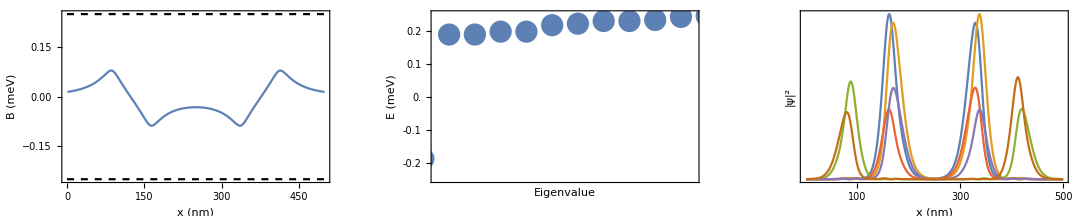

```mathematica
t=6;
GraphicsRow[{ListPlot[{magplt[[t]],{{0,Δ},{500,Δ}},{{0,-Δ},{500,-Δ}}},PlotRange->All,Joined->True,Frame->True,FrameLabel->{{"B (meV)",None},{"x (nm)",None}},LabelStyle->{Black,20},PlotStyle->{Back,{Black,Dashed},{Black,Dashed}}],ListPlot[eplt[[t]],PlotRange->{{1000.5,1010.5},{-Δ,Δ}},PlotStyle->{PointSize[0.04]},Frame->True,FrameLabel->{{"E (meV)",None},{"Eigenvalue",None}},LabelStyle->{Black,20},FrameTicks->{{{-0.2,-0.1,0.0,0.1,0.2},None},{None,None}}],ListPlot[Pplt[[t]],Joined->True,PlotRange->All,Frame->True,FrameLabel->{{"|ψ|^2",None},{"x (nm)",None}},LabelStyle->{Black,20},FrameTicks->{{None,None},{{100,200,300,400,500},None}}]}]
```

```mathematica
line=Table[{1003.5+0.000001*i,-0.3+0.02*i},{i,0,30}];
Manipulate[GraphicsRow[{ListPlot[{magplt[[t]],{{0,Δ},{500,Δ}},{{0,-Δ},{500,-Δ}}},PlotRange->All,Joined->True,Frame->True,FrameLabel->{{"B (meV)",None},{"x (nm)",None}},LabelStyle->{Black,20},PlotStyle->{Back,{Black,Dashed},{Black,Dashed}}],ListPlot[{eplt[[t]],line},PlotRange->{{1000.5,1010.5},{-Δ,Δ}},PlotStyle->{PointSize[0.04],{Black,PointSize[0.01]}},Frame->True,FrameLabel->{{"E (meV)",None},{"Eigenvalue",None}},LabelStyle->{Black,20},FrameTicks->{{{-0.2,-0.1,0.0,0.1,0.2},None},{None,None}}],ListPlot[Pplt[[t]],Joined->True,PlotRange->All,Frame->True,FrameLabel->{{"|ψ|^2",None},{"x (nm)",None}},LabelStyle->{Black,20},FrameTicks->{{None,None},{{100,200,300,400,500},None}}]}],{t,1,Length[eplt],1}]
```

```mathematica
magpltI=Import["C:\\Users\\jsten\\Documents\\Reaserch\\Majorana spin\\Magnetic Profile\\data\\mag.mx"];
epltI=Import["C:\\Users\\jsten\\Documents\\Reaserch\\Majorana spin\\Magnetic Profile\\data\\e.mx"];
PpltI=Import["C:\\Users\\jsten\\Documents\\Reaserch\\Majorana spin\\Magnetic Profile\\data\\P.mx"];
```

```mathematica
t=6;
GraphicsRow[{ListPlot[{magplt[[t]],{{0,Δ},{500,Δ}},{{0,-Δ},{500,-Δ}}},PlotRange->All,Joined->True,Frame->True,FrameLabel->{{"B (meV)",None},{"x (nm)",None}},LabelStyle->{Black,20},PlotStyle->{Back,{Black,Dashed},{Black,Dashed}}],ListPlot[eplt[[t]],PlotRange->{{1000.5,1010.5},{-Δ,Δ}},PlotStyle->{PointSize[0.04]},Frame->True,FrameLabel->{{"E (meV)",None},{"Eigenvalue",None}},LabelStyle->{Black,20},FrameTicks->{{{-0.2,-0.1,0.0,0.1,0.2},None},{None,None}}],ListPlot[Pplt[[t]],Joined->True,PlotRange->All,Frame->True,FrameLabel->{{"|ψ|^2",None},{"x (nm)",None}},LabelStyle->{Black,20},FrameTicks->{{None,None},{{100,200,300,400,500},None}}]}]
```

-Graphics-

```mathematica
line=Table[{1003.5+0.000001*i,-0.3+0.02*i},{i,0,30}];
Manipulate[GraphicsRow[{ListPlot[{magplt[[t]],{{0,Δ},{500,Δ}},{{0,-Δ},{500,-Δ}}},PlotRange->All,Joined->True,Frame->True,FrameLabel->{{"B (meV)",None},{"x (nm)",None}},LabelStyle->{Black,20},PlotStyle->{Back,{Black,Dashed},{Black,Dashed}}],ListPlot[{eplt[[t]],line},PlotRange->{{1000.5,1010.5},{-Δ,Δ}},PlotStyle->{PointSize[0.04],{Black,PointSize[0.01]}},Frame->True,FrameLabel->{{"E (meV)",None},{"Eigenvalue",None}},LabelStyle->{Black,20},FrameTicks->{{{-0.2,-0.1,0.0,0.1,0.2},None},{None,None}}],ListPlot[Pplt[[t]],Joined->True,PlotRange->All,Frame->True,FrameLabel->{{"|ψ|^2",None},{"x (nm)",None}},LabelStyle->{Black,20},FrameTicks->{{None,None},{{100,200,300,400,500},None}}]}],{t,1,Length[eplt],1}]
```